Associations

Associations are a kind of generalization of lists, in which every element has a key as well as a value. Counts is a typical function that produces an association.

Counts gives an association that reports how many times each different element occurs:

```mathematica
Counts[{a,a,b,c,a,a,b,c,c,a,a}]
```

<|a→6,b→2,c→3|>

You can get the value associated with a particular key using [...].

Find the value associated with c in the association:

```mathematica
<|a->6,b->2,c->3|>[c]
```

3

Operations that work on lists typically also work on associations—but apply themselves only to the values, not the keys.

This adds 500 to each value in the association:

```mathematica
<|a->6,b->2,c->3|>+500
```

<|a→506,b→502,c→503|>

/@ applies a function to each value in the association:

```mathematica
f/@<|a->6,b->2,c->3|>
```

<|a→f[6],b→f[2],c→f[3]|>

Total gives the total of the values:

```mathematica
Total[<|a->6,b->2,c->3|>]
```

11

Sort operates on the values:

```mathematica
Sort[<|a->6,b->2,c->3|>]
```

<|b→2,c→3,a→6|>

KeySort operates on the keys:

```mathematica
KeySort[<|c->1,b->2,a->4|>]
```

<|a→4,b→2,c→1|>

The functions Keys and Values extract the keys and values of an association.

Get the list of keys in the association:

```mathematica
Keys[<|a->6,b->2,c->3|>]
```

{a,b,c}

Get the list of values in the association:

```mathematica
Values[<|a->6,b->2,c->3|>]
```

{6,2,3}

Normal turns an association into a normal list of rules. Association makes an association from a list of rules.

```mathematica
Normal[<|a->6,b->2,c->3|>]
```

{a→6,b→2,c→3}

```mathematica
Association[{a->6,b->2,c->3}]
```

<|a→6,b→2,c→3|>

LetterCounts counts how many times letters occur in a string.

Count how many times each letter occurs in the Wikipedia article on computers:

```mathematica
LetterCounts[WikipediaData["computers"]]
```

<|e→5482,t→4016,a→3565,o→3480,r→3290,i→3234,n→3128,s→2838,c→2086,l→1918,m→1678,h→1645,d→1548,u→1530,p→1312,g→916,f→845,y→695,b→608,w→525,v→433,k→220,T→180,C→137,I→125,A→125,S→116,M→115,x→93,P→86,O→64,q→61,E→60,U→58,B→54,R→54,H→50,D→44,W→40,z→40,N→39,L→39,F→34,j→29,J→22,G→22,K→18,Z→15,V→9,ī→4,ū→4,Q→2,ā→2,X→1,â→1,é→1,Y→1|>

KeyTake picks out elements of an association that appear in a list of keys you specify. Here we’re taking the elements whose keys are letters in the (lowercase) alphabet.

Take only those elements in the association whose keys appear as letters in the alphabet:

```mathematica
KeyTake[LetterCounts[WikipediaData["computers"]],Alphabet[ ]]
```

<|a→3565,b→608,c→2086,d→1548,e→5482,f→845,g→916,h→1645,i→3234,j→29,k→220,l→1918,m→1678,n→3128,o→3480,p→1312,q→61,r→3290,s→2838,t→4016,u→1530,v→433,w→525,x→93,y→695,z→40|>

BarChart plots the values in an association. With the option ChartLabels→Automatic, it uses the keys as labels.

Make a bar chart of how many times each letter appears; “e” is the most common:

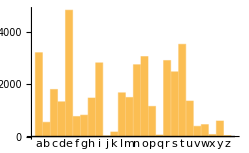

```mathematica
BarChart[KeyTake[LetterCounts[WikipediaData["computers"]],Alphabet[ ]],ChartLabels->Automatic]
```

Here’s a direct way to apply a pure function to an association.

Apply a pure function to an association:

```mathematica
f[#["apples"],#["oranges"]]&[<|"apples"->10,"oranges"->12,"pears"->4|>]
```

f[10,12]

It’s very common to have keys that are strings, and the Wolfram Language has a special way to handle these when it comes to pure functions: you can just use #key to refer to an element whose key is "key".

Use the simpler notation for association elements whose keys are strings:

```mathematica
f[#apples,#oranges]&[<|"apples"->10,"oranges"->12,"pears"->4|>]
```

f[10,12]

As a more realistic example, apply a pure function that extracts the value for “e” from the letter counts, and divides by the total. The N gives the result as a decimal.

Compute the fraction of letters in the “computers” article that are “e”:

```mathematica
#e/Total[#]& @LetterCounts[WikipediaData["computers"]]//N
```

0.117295

Vocabulary

<|key_1→value_1,key_2→value_2, ...|> |   | an association
Association[rules] |   | turn a list of rules into an association
assoc[key] |   | extract an element of an association
Keys[assoc] |   | list of keys in an association
Values[assoc] |   | list of values in an association
Normal[assoc] |   | turn an association into a list of rules
KeySort[assoc] |   | sort an association by its keys
KeyTake[assoc,keys] |   | take elements with particular keys
#key |   | function slot for an element with key “key”
Counts[list] |   | an association with counts of distinct elements
LetterCounts[string] |   | an association with counts of distinct letters

"6 Exercises Available" | "Get Started »"

Make a list, in order, of the number of times each of the digits 0 through 9 occurs in 3^100. »

| Expected output: |  
  | {7,9,9,5,1,5,4,7,1} |

Make a labeled bar chart of the number of times each of the digits 0 through 9 occurs in 2^1000. »

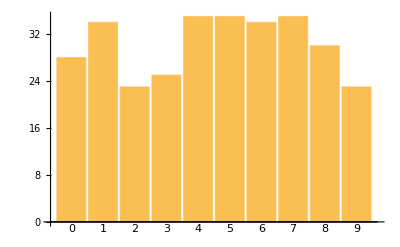
| Expected output: |  
  | -Graphics- |

Make a labeled bar chart of the number of times each possible first letter occurs in words from WordList[ ], with all letters made uppercase. »

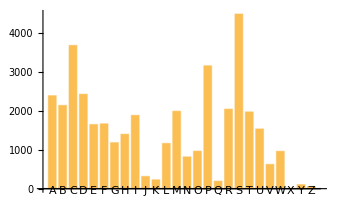
| Expected output: |  
  | -Graphics- |

Make an association giving the 5 most common first letters of words in WordList[ ] and their counts. »

| Expected output: |  
  | <|"s"→4499,"c"→3693,"p"→3168,"d"→2433,"a"→2393|> |

Find the numerical ratio of the number of occurrences of “q” and “u” in the Wikipedia entry for computers. »

| Sample expected output: |  
  | 0.0398693 |

Find the 10 most common words in ExampleData[{"Text","AliceInWonderland"}]. »

| Expected output: |  
  | {"the","and","a","to","she","of","was","Alice","in","it"} |

Q&A

Why are associations called “associations”?

Because they associate values with keys. Other names used for the same concept are associative arrays, dictionaries, hashmaps, structs, key-value maps and symbolically indexed lists.

How does one type in an association?

Start with <| (< followed by |), then use -> for each →. Alternatively use Association[a->1,b->2].

Can an association have several elements with the same key?

No. Keys in an association are always unique.

What happens if I ask for a key that’s not in an association?

Normally you get Missing[...]. But if you use Lookup to look up the key, you can specify what to return if the key is absent.

How can I do operations on the keys of an association?

Use KeyMap, or use functions like KeySelect and KeyDrop. AssociationMap creates an association by mapping a function over keys.

How can I combine several associations into one?

Use Merge. You have to give a function to say what to do if the same key occurs in multiple associations.

Can one use [[...]] to extract part of an association, like one extracts part of a list?

Yes, if you explicitly say assoc[[Key[key]]]. For example, assoc[[2]] will extract the second element of assoc, whatever key it has. assoc[[key]] is a special case that works the same as assoc[key].

What happens in pure functions if the keys in an association aren’t strings?

You can’t use #key anymore; you have to explicitly use #[key].

Tech Notes

Most functions effectively operate on associations as if they were operating on lists of their values. Functions that thread themselves over lists typically do the same over associations.

Associations are like tables in a relational database. JoinAcross does the analog of a database join.

More to Explore

Guide to Associations in the Wolfram Language »